## Para 10 posições

```mathematica
w=1
h= ({{0, v, 0, 0, 0, 0, 0, 0, 0, 0}, {v, 0, w, 0, 0, 0, 0, 0, 0, 0}, {0, w, 0, v, 0, 0, 0, 0, 0, 0}, {0, 0, v, 0, w, 0, 0, 0, 0, 0}, {0, 0, 0, w, 0, v, 0, 0, 0, 0}, {0, 0, 0, 0, v, 0, w, 0, 0, 0}, {0, 0, 0, 0, 0, w, 0, v, 0, 0}, {0, 0, 0, 0, 0, 0, v, 0, w, 0}, {0, 0, 0, 0, 0, 0, 0, w, 0, v}, {0, 0, 0, 0, 0, 0, 0, 0, v, 0}})
(*valores=Table[Eigenvalues[h],{v,0.,3.,.1}];*)
```

1

{{0,v,0,0,0,0,0,0,0,0},{v,0,1,0,0,0,0,0,0,0},{0,1,0,v,0,0,0,0,0,0},{0,0,v,0,1,0,0,0,0,0},{0,0,0,1,0,v,0,0,0,0},{0,0,0,0,v,0,1,0,0,0},{0,0,0,0,0,1,0,v,0,0},{0,0,0,0,0,0,v,0,1,0},{0,0,0,0,0,0,0,1,0,v},{0,0,0,0,0,0,0,0,v,0}}

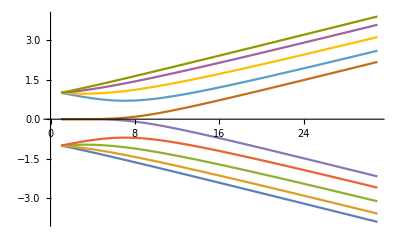

```mathematica
(*ListPlot[(Sort[#]&/@valores)//Transpose,Joined->True]*)
```

```mathematica
{valores,vetores}=Table[Eigensystem[h],{v,0,3,0.1}]
```

Set::shape: Lists {valores, vetores} and {{{1., 1., 1., 1., -1., -1., -1., -1., 0., 0.}, {« 1 »}}, « 29 », {{-3.88946, 3.88946, « 7 », 2.16758}, {« 1 »}}} are not the same shape.

{{{1.,1.,1.,1.,-1.,-1.,-1.,-1.,0.,0.},{{0.,0.,0.,0.,0.,0.707107,0.707107,0.,0.,0.},{0.,0.,0.,0.707107,0.707107,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.707107,0.707107,0.},{0.,0.707107,0.707107,0.,0.,0.,0.,0.,0.,0.},{0.,0.707107,-0.707107,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.707107,-0.707107,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.707107,-0.707107,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.707107,-0.707107,0.},{1.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,1.}}},{{1.08308,-1.08308,1.03695,-1.03695,0.975677,-0.975677,0.921812,-0.921812,9.9×10^-6,-9.9×10^-6},{{0.0237271,0.256982,0.275959,0.419015,0.426228,0.426228,0.419015,0.275959,0.256982,0.0237271},{-0.0237271,0.256982,-0.275959,0.419015,-0.426228,0.426228,-0.419015,0.275959,-0.256982,0.0237271},{0.0406061,0.421065,0.432563,0.274811,0.241709,-0.241709,-0.274811,-0.432563,-0.421065,-0.0406061},{-0.0406061,0.421065,-0.432563,0.274811,-0.241709,-0.241709,0.274811,-0.432563,0.421065,-0.0406061},{0.0439506,0.428816,0.413991,-0.248947,-0.284291,-0.284291,-0.248947,0.413991,0.428816,0.0439506},{0.0439506,-0.428816,0.413991,0.248947,-0.284291,0.284291,-0.248947,-0.413991,0.428816,-0.0439506},{-0.0292661,-0.269778,-0.245758,0.432355,0.423126,-0.423126,-0.432355,0.245758,0.269778,0.0292661},{0.0292661,-0.269778,0.245758,0.432355,-0.423126,-0.423126,0.432355,0.245758,-0.269778,0.0292661},{0.703562,0.0000696527,-0.0703562,-0.000703492,0.00703562,0.00703562,-0.000703492,-0.0703562,0.0000696527,0.703562},{0.703562,-0.0000696527,-0.0703562,0.000703492,0.00703562,-0.00703562,-0.000703492,0.0703562,0.0000696527,-0.703562}}},{{1.16968,-1.16968,1.08479,-1.08479,0.965281,-0.965281,0.850473,-0.850473,0.0003072,-0.0003072},{{0.0430884,0.251998,0.286139,0.413465,0.426394,0.426394,0.413465,0.286139,0.251998,0.0430884},{-0.0430884,0.251998,-0.286139,0.413465,-0.426394,0.426394,-0.413465,0.286139,-0.251998,0.0430884},{0.0767772,0.416437,0.436393,0.284797,0.221668,-0.221668,-0.284797,-0.436393,-0.416437,-0.0767772},{0.0767772,-0.416437,0.436393,-0.284797,0.221668,0.221668,-0.284797,0.436393,-0.416437,0.0767772},{0.0893387,0.431185,0.398347,-0.233341,-0.304909,-0.304909,-0.233341,0.398347,0.431185,0.0893387},{-0.0893387,0.431185,-0.398347,-0.233341,0.304909,-0.304909,0.233341,0.398347,-0.431185,0.0893387},{0.0653209,0.277768,0.22317,-0.439839,-0.418706,0.418706,0.439839,-0.22317,-0.277768,-0.0653209},{0.0653209,-0.277768,0.22317,0.439839,-0.418706,-0.418706,0.439839,0.22317,-0.277768,0.0653209},{0.692821,0.00106417,-0.138564,-0.0055337,0.0277111,0.0277111,-0.0055337,-0.138564,0.00106417,0.692821},{-0.692821,0.00106417,0.138564,-0.0055337,-0.0277111,0.0277111,0.0055337,-0.138564,-0.00106417,0.692821}}},{{1.25888,-1.25888,1.1417,-1.1417,0.96935,-0.96935,0.788734,-0.788734,0.00221136,-0.00221136},{{0.0590446,0.247766,0.294194,0.408624,0.426148,0.426148,0.408624,0.294194,0.247766,0.0590446},{-0.0590446,0.247766,-0.294194,0.408624,-0.426148,0.426148,-0.408624,0.294194,-0.247766,0.0590446},{0.108201,0.411778,0.437668,0.29303,0.203252,-0.203252,-0.29303,-0.437668,-0.411778,-0.108201},{-0.108201,0.411778,-0.437668,0.29303,-0.203252,-0.203252,0.29303,-0.437668,0.411778,-0.108201},{0.133779,0.432262,0.378879,-0.216652,-0.323675,-0.323675,-0.216652,0.378879,0.432262,0.133779},{-0.133779,0.432262,-0.378879,-0.216652,0.323675,-0.323675,0.216652,0.378879,-0.432262,0.133779},{-0.109034,-0.286663,-0.193391,0.447097,0.410658,-0.410658,-0.447097,0.193391,0.286663,0.109034},{0.109034,-0.286663,0.193391,0.447097,-0.410658,-0.410658,0.447097,0.193391,-0.286663,0.109034},{0.674552,0.00497226,-0.202355,-0.0180658,0.0606665,0.0606665,-0.0180658,-0.202355,0.00497226,0.674552},{-0.674552,0.00497226,0.202355,-0.0180658,-0.0606665,0.0606665,0.0180658,-0.202355,-0.00497226,0.674552}}},{{1.35002,-1.35002,1.20599,-1.20599,0.987508,-0.987508,0.740142,-0.740142,0.00860525,-0.00860525},{{0.0723412,0.244154,0.300675,0.404405,0.425683,0.425683,0.404405,0.300675,0.244154,0.0723412},{-0.0723412,0.244154,-0.300675,0.404405,-0.425683,0.425683,-0.404405,0.300675,-0.244154,0.0723412},{-0.135098,-0.407316,-0.437178,-0.299788,-0.186669,0.186669,0.299788,0.437178,0.407316,0.135098},{-0.135098,0.407316,-0.437178,0.299788,-0.186669,-0.186669,0.299788,-0.437178,0.407316,-0.135098},{0.175038,0.43213,0.356716,-0.199674,-0.339866,-0.339866,-0.199674,0.356716,0.43213,0.175038},{0.175038,-0.43213,0.356716,0.199674,-0.339866,0.339866,-0.199674,-0.356716,0.43213,-0.175038},{0.159911,0.295892,0.155038,-0.452855,-0.397192,0.397192,0.452855,-0.155038,-0.295892,-0.159911},{0.159911,-0.295892,0.155038,0.452855,-0.397192,-0.397192,0.452855,0.155038,-0.295892,0.159911},{0.64831,0.0139472,-0.259204,-0.0404442,0.103333,0.103333,-0.0404442,-0.259204,0.0139472,0.64831},{0.64831,-0.0139472,-0.259204,0.0404442,0.103333,-0.103333,-0.0404442,0.259204,0.0139472,-0.64831}}},{{1.44264,-1.44264,1.2762,-1.2762,1.01859,-1.01859,0.708547,-0.708547,0.0235183,-0.0235183},{{0.0835452,0.24105,0.305975,0.400721,0.425107,0.425107,0.400721,0.305975,0.24105,0.0835452},{0.0835452,-0.24105,0.305975,-0.400721,0.425107,-0.425107,0.400721,-0.305975,0.24105,-0.0835452},{-0.157959,-0.403175,-0.435552,-0.305351,-0.171913,0.171913,0.305351,0.435552,0.403175,0.157959},{-0.157959,0.403175,-0.435552,0.305351,-0.171913,-0.171913,0.305351,-0.435552,0.403175,-0.157959},{0.211601,0.43107,0.333284,-0.183181,-0.353228,-0.353228,-0.183181,0.333284,0.43107,0.211601},{-0.211601,0.43107,-0.333284,-0.183181,0.353228,-0.353228,0.183181,0.333284,-0.43107,0.211601},{0.21484,0.304448,0.108296,-0.455431,-0.376842,0.376842,0.455431,-0.108296,-0.304448,-0.21484},{-0.21484,0.304448,-0.108296,-0.455431,0.376842,0.376842,-0.455431,-0.108296,0.304448,-0.21484},{0.614115,0.028886,-0.306378,-0.072183,0.151492,0.151492,-0.072183,-0.306378,0.028886,0.614115},{0.614115,-0.028886,-0.306378,0.072183,0.151492,-0.151492,-0.072183,0.306378,0.028886,-0.614115}}},{{1.53641,-1.53641,1.35116,-1.35116,1.06096,-1.06096,0.696868,-0.696868,0.0506635,-0.0506635},{{0.0930861,0.238364,0.310372,0.397491,0.424485,0.424485,0.397491,0.310372,0.238364,0.0930861},{-0.0930861,0.238364,-0.310372,0.397491,-0.424485,0.424485,-0.397491,0.310372,-0.238364,0.0930861},{0.177362,0.399408,0.433247,0.309962,0.158861,-0.158861,-0.309962,-0.433247,-0.399408,-0.177362},{0.177362,-0.399408,0.433247,-0.309962,0.158861,0.158861,-0.309962,0.433247,-0.399408,0.177362},{0.242858,0.429435,0.309897,-0.167746,-0.36391,-0.36391,-0.167746,0.309897,0.429435,0.242858},{0.242858,-0.429435,0.309897,0.167746,-0.36391,0.36391,-0.167746,-0.309897,0.429435,-0.242858},{0.268011,0.31128,0.0561144,-0.453626,-0.349786,0.349786,0.453626,-0.0561144,-0.31128,-0.268011},{0.268011,-0.31128,0.0561144,0.453626,-0.349786,-0.349786,0.453626,0.0561144,-0.31128,0.268011},{0.573645,0.0484381,-0.341733,-0.109586,0.199488,0.199488,-0.109586,-0.341733,0.0484381,0.573645},{0.573645,-0.0484381,-0.341733,0.109586,0.199488,-0.199488,-0.109586,0.341733,0.0484381,-0.573645}}},{{1.63109,-1.63109,1.42993,-1.42993,1.11282,-1.11282,0.705732,-0.705732,0.0917556,-0.0917556},{{0.101291,0.236021,0.314068,0.394645,0.423853,0.423853,0.394645,0.314068,0.236021,0.101291},{-0.101291,0.236021,-0.314068,0.394645,-0.423853,0.423853,-0.394645,0.314068,-0.236021,0.101291},{-0.193865,-0.396019,-0.430575,-0.313819,-0.147338,0.147338,0.313819,0.430575,0.396019,0.193865},{0.193865,-0.396019,0.430575,-0.313819,0.147338,0.147338,-0.313819,0.430575,-0.396019,0.193865},{0.268935,0.427537,0.287517,-0.153689,-0.37229,-0.37229,-0.153689,0.287517,0.427537,0.268935},{0.268935,-0.427537,0.287517,0.153689,-0.37229,0.37229,-0.153689,-0.287517,0.427537,-0.268935},{0.313403,0.315969,0.00360785,-0.447747,-0.318515,0.318515,0.447747,-0.00360785,-0.315969,-0.313403},{0.313403,-0.315969,0.00360785,0.447747,-0.318515,-0.318515,0.447747,0.00360785,-0.315969,0.313403},{0.530669,0.0695598,-0.365086,-0.147226,0.242051,0.242051,-0.147226,-0.365086,0.0695598,0.530669},{-0.530669,0.0695598,0.365086,-0.147226,-0.242051,0.242051,0.147226,-0.365086,-0.0695598,0.530669}}},{{1.7265,-1.7265,1.51178,-1.51178,1.1725,-1.1725,0.733248,-0.733248,0.146027,-0.146027},{{0.108411,0.233964,0.31721,0.392123,0.423231,0.423231,0.392123,0.31721,0.233964,0.108411},{-0.108411,0.233964,-0.31721,0.392123,-0.423231,0.423231,-0.392123,0.31721,-0.233964,0.108411},{0.207961,0.392988,0.427741,0.317078,0.137157,-0.137157,-0.317078,-0.427741,-0.392988,-0.207961},{0.207961,-0.392988,0.427741,-0.317078,0.137157,0.137157,-0.317078,0.427741,-0.392988,0.207961},{0.290386,0.425598,0.266705,-0.141108,-0.378813,-0.378813,-0.141108,0.266705,0.425598,0.290386},{0.290386,-0.425598,0.266705,0.141108,-0.378813,0.378813,-0.141108,-0.266705,0.425598,-0.290386},{-0.347944,-0.318911,0.0445139,0.439439,0.286606,-0.286606,-0.439439,-0.0445139,0.318911,0.347944},{0.347944,-0.318911,-0.0445139,0.439439,-0.286606,-0.286606,0.439439,-0.0445139,-0.318911,0.347944},{0.4895,0.0893501,-0.378553,-0.180786,0.276443,0.276443,-0.180786,-0.378553,0.0893501,0.4895},{-0.4895,0.0893501,0.378553,-0.180786,-0.276443,0.276443,0.180786,-0.378553,-0.0893501,0.4895}}},{{1.8225,-1.8225,1.59612,-1.59612,1.23854,-1.23854,0.776097,-0.776097,0.211181,-0.211181},{{0.11464,0.232147,0.319911,0.389878,0.422632,0.422632,0.389878,0.319911,0.232147,0.11464},{0.11464,-0.232147,0.319911,-0.389878,0.422632,-0.422632,0.389878,-0.319911,0.232147,-0.11464},{0.220068,0.390283,0.424877,0.319858,0.128142,-0.128142,-0.319858,-0.424877,-0.390283,-0.220068},{0.220068,-0.390283,0.424877,-0.319858,0.128142,0.128142,-0.319858,0.424877,-0.390283,0.220068},{0.307924,0.423751,0.247699,-0.129962,-0.383892,-0.383892,-0.129962,0.247699,0.423751,0.307924},{0.307924,-0.423751,0.247699,0.129962,-0.383892,0.383892,-0.129962,-0.247699,0.423751,-0.307924},{-0.372037,-0.320819,0.0858468,0.430494,0.256843,-0.256843,-0.430494,-0.0858468,0.320819,0.372037},{0.372037,-0.320819,-0.0858468,0.430494,-0.256843,-0.256843,0.430494,-0.0858468,-0.320819,0.372037},{0.452989,0.106292,-0.385243,-0.208497,0.302688,0.302688,-0.208497,-0.385243,0.106292,0.452989},{-0.452989,0.106292,0.385243,-0.208497,-0.302688,0.302688,0.208497,-0.385243,-0.106292,0.452989}}},{{1.91899,-1.91899,1.68251,-1.68251,1.30972,-1.30972,0.83083,-0.83083,0.28463,-0.28463},{{0.120131,0.23053,0.322253,0.387868,0.422061,0.422061,0.387868,0.322253,0.23053,0.120131},{0.120131,-0.23053,0.322253,-0.387868,0.422061,-0.422061,0.387868,-0.322253,0.23053,-0.120131},{0.23053,0.387868,0.422061,0.322253,0.120131,-0.120131,-0.322253,-0.422061,-0.387868,-0.23053},{0.23053,-0.387868,0.422061,-0.322253,0.120131,0.120131,-0.322253,0.422061,-0.387868,0.23053},{-0.322253,-0.422061,-0.23053,0.120131,0.387868,0.387868,0.120131,-0.23053,-0.422061,-0.322253},{-0.322253,0.422061,-0.23053,-0.120131,0.387868,-0.387868,0.120131,0.23053,-0.422061,0.322253},{0.387868,0.322253,-0.120131,-0.422061,-0.23053,0.23053,0.422061,0.120131,-0.322253,-0.387868},{0.387868,-0.322253,-0.120131,0.422061,-0.23053,-0.23053,0.422061,-0.120131,-0.322253,0.387868},{0.422061,0.120131,-0.387868,-0.23053,0.322253,0.322253,-0.23053,-0.387868,0.120131,0.422061},{0.422061,-0.120131,-0.387868,0.23053,0.322253,-0.322253,-0.23053,0.387868,0.120131,-0.422061}}},{{2.01588,-2.01588,1.77058,-1.77058,-1.38508,1.38508,0.894545,-0.894545,0.364172,-0.364172},{{0.125004,0.229084,0.324301,0.386061,0.421521,0.421521,0.386061,0.324301,0.229084,0.125004},{-0.125004,0.229084,-0.324301,0.386061,-0.421521,0.421521,-0.386061,0.324301,-0.229084,0.125004},{0.239628,0.385711,0.419341,0.324334,0.112986,-0.112986,-0.324334,-0.419341,-0.385711,-0.239628},{0.239628,-0.385711,0.419341,-0.324334,0.112986,0.112986,-0.324334,0.419341,-0.385711,0.239628},{-0.333994,0.420553,-0.215105,-0.111468,0.391008,-0.391008,0.111468,0.215105,-0.420553,0.333994},{-0.333994,-0.420553,-0.215105,0.111468,0.391008,0.391008,0.111468,-0.215105,-0.420553,-0.333994},{-0.397813,-0.323511,0.148199,0.41462,0.207877,-0.207877,-0.41462,-0.148199,0.323511,0.397813},{0.397813,-0.323511,-0.148199,0.41462,-0.207877,-0.207877,0.41462,-0.148199,-0.323511,0.397813},{0.396415,0.131239,-0.388263,-0.247849,0.33683,0.33683,-0.247849,-0.388263,0.131239,0.396415},{0.396415,-0.131239,-0.388263,0.247849,0.33683,-0.33683,-0.247849,0.388263,0.131239,-0.396415}}},{{2.11311,-2.11311,1.86006,-1.86006,-1.46384,1.46384,0.96503,-0.96503,0.44815,-0.44815},{{0.129355,0.227784,0.326107,0.384429,0.421011,0.421011,0.384429,0.326107,0.227784,0.129355},{0.129355,-0.227784,0.326107,-0.384429,0.421011,-0.421011,0.384429,-0.326107,0.227784,-0.129355},{-0.24759,-0.383777,-0.416743,-0.326159,-0.106586,0.106586,0.326159,0.416743,0.383777,0.24759},{0.24759,-0.383777,0.416743,-0.326159,0.106586,0.106586,-0.326159,0.416743,-0.383777,0.24759},{0.343666,-0.419225,0.201278,0.103823,-0.393513,0.393513,-0.103823,-0.201278,0.419225,-0.343666},{0.343666,0.419225,0.201278,-0.103823,-0.393513,-0.393513,-0.103823,0.201278,0.419225,0.343666},{-0.403776,-0.324713,0.171173,0.408251,0.188566,-0.188566,-0.408251,-0.171173,0.324713,0.403776},{0.403776,-0.324713,-0.171173,0.408251,-0.188566,-0.188566,0.408251,-0.171173,-0.324713,0.403776},{-0.375267,-0.140147,0.387514,0.261509,-0.347821,-0.347821,0.261509,0.387514,-0.140147,-0.375267},{-0.375267,0.140147,0.387514,-0.261509,-0.347821,0.347821,0.261509,-0.387514,-0.140147,0.375267}}},{{2.21063,-2.21063,1.95073,-1.95073,1.54538,-1.54538,1.04066,-1.04066,0.535379,-0.535379},{{0.133262,0.22661,0.327709,0.382947,0.420532,0.420532,0.382947,0.327709,0.22661,0.133262},{0.133262,-0.22661,0.327709,-0.382947,0.420532,-0.420532,0.382947,-0.327709,0.22661,-0.133262},{-0.254598,-0.38204,-0.414277,-0.32777,-0.10083,0.10083,0.32777,0.414277,0.38204,0.254598},{-0.254598,0.38204,-0.414277,0.32777,-0.10083,-0.10083,0.32777,-0.414277,0.38204,-0.254598},{0.351683,0.418064,0.18888,-0.0970556,-0.395532,-0.395532,-0.0970556,0.18888,0.418064,0.351683},{0.351683,-0.418064,0.18888,0.0970556,-0.395532,0.395532,-0.0970556,-0.18888,0.418064,-0.351683},{-0.407108,-0.325893,0.190097,0.402861,0.172114,-0.172114,-0.402861,-0.190097,0.325893,0.407108},{0.407108,-0.325893,-0.190097,0.402861,-0.172114,-0.172114,0.402861,-0.190097,-0.325893,0.407108},{0.357775,0.147343,-0.386224,-0.272399,0.356254,0.356254,-0.272399,-0.386224,0.147343,0.357775},{0.357775,-0.147343,-0.386224,0.272399,0.356254,-0.356254,-0.272399,0.386224,0.147343,-0.357775}}},{{2.30839,-2.30839,2.04239,-2.04239,1.62923,-1.62923,1.12025,-1.12025,0.625023,-0.625023},{{0.136789,0.225544,0.329139,0.381598,0.420082,0.420082,0.381598,0.329139,0.225544,0.136789},{-0.136789,0.225544,-0.329139,0.381598,-0.420082,0.420082,-0.381598,0.329139,-0.225544,0.136789},{0.260804,0.380473,0.411948,0.329203,0.0956321,-0.0956321,-0.329203,-0.411948,-0.380473,-0.260804},{0.260804,-0.380473,0.411948,-0.329203,0.0956321,0.0956321,-0.329203,0.411948,-0.380473,0.260804},{0.358375,0.417053,0.177748,-0.0910435,-0.397178,-0.397178,-0.0910435,0.177748,0.417053,0.358375},{-0.358375,0.417053,-0.177748,-0.0910435,0.397178,-0.397178,0.0910435,0.177748,-0.417053,0.358375},{-0.408717,-0.327047,0.205829,0.398305,0.158042,-0.158042,-0.398305,-0.205829,0.327047,0.408717},{0.408717,-0.327047,-0.205829,0.398305,-0.158042,-0.158042,0.398305,-0.205829,-0.327047,0.408717},{-0.343202,-0.153221,0.384716,0.281198,-0.362847,-0.362847,0.281198,0.384716,-0.153221,-0.343202},{0.343202,-0.153221,-0.384716,0.281198,0.362847,-0.362847,-0.281198,0.384716,0.153221,-0.343202}}},{{2.40636,-2.40636,2.1349,-2.1349,1.71499,-1.71499,1.20294,-1.20294,0.716491,-0.716491},{{0.139987,0.224573,0.330423,0.380364,0.41966,0.41966,0.380364,0.330423,0.224573,0.139987},{-0.139987,0.224573,-0.330423,0.380364,-0.41966,0.41966,-0.380364,0.330423,-0.224573,0.139987},{0.266329,0.379057,0.409754,0.330485,0.0909199,-0.0909199,-0.330485,-0.409754,-0.379057,-0.266329},{0.266329,-0.379057,0.409754,-0.330485,0.0909199,0.0909199,-0.330485,0.409754,-0.379057,0.266329},{0.364002,0.416173,0.167729,-0.0856801,-0.398533,-0.398533,-0.0856801,0.167729,0.416173,0.364002},{-0.364002,0.416173,-0.167729,-0.0856801,0.398533,-0.398533,0.0856801,0.167729,-0.416173,0.364002},{0.409205,0.328167,-0.21904,-0.39444,-0.14593,0.14593,0.39444,0.21904,-0.328167,-0.409205},{0.409205,-0.328167,-0.21904,0.39444,-0.14593,-0.14593,0.39444,-0.21904,-0.328167,0.409205},{-0.330948,-0.158081,0.383158,0.288407,-0.368097,-0.368097,0.288407,0.383158,-0.158081,-0.330948},{0.330948,-0.158081,-0.383158,0.288407,0.368097,-0.368097,-0.288407,0.383158,0.158081,-0.330948}}},{{2.50452,-2.50452,2.22814,-2.22814,-1.80236,1.80236,1.2881,-1.2881,0.80936,-0.80936},{{0.142899,0.223684,0.331582,0.379232,0.419263,0.419263,0.379232,0.331582,0.223684,0.142899},{0.142899,-0.223684,0.331582,-0.379232,0.419263,-0.419263,0.379232,-0.331582,0.223684,-0.142899},{0.271272,0.377771,0.407691,0.331638,0.0866317,-0.0866317,-0.331638,-0.407691,-0.377771,-0.271272},{0.271272,-0.377771,0.407691,-0.331638,0.0866317,0.0866317,-0.331638,0.407691,-0.377771,0.271272},{0.368766,-0.415406,0.158684,0.0808748,-0.39966,0.39966,-0.0808748,-0.158684,0.415406,-0.368766},{0.368766,0.415406,0.158684,-0.0808748,-0.39966,-0.39966,-0.0808748,0.158684,0.415406,0.368766},{-0.408966,-0.329243,0.230247,0.39114,0.135432,-0.135432,-0.39114,-0.230247,0.329243,0.408966},{0.408966,-0.329243,-0.230247,0.39114,-0.135432,-0.135432,0.39114,-0.230247,-0.329243,0.408966},{-0.320546,-0.162148,0.381637,0.294394,-0.372349,-0.372349,0.294394,0.381637,-0.162148,-0.320546},{0.320546,-0.162148,-0.381637,0.294394,0.372349,-0.372349,-0.294394,0.381637,0.162148,-0.320546}}},{{2.60284,-2.60284,2.32201,-2.32201,1.89109,-1.89109,1.37524,-1.37524,0.903324,-0.903324},{{0.145563,0.222868,0.332633,0.37819,0.41889,0.41889,0.37819,0.332633,0.222868,0.145563},{-0.145563,0.222868,-0.332633,0.37819,-0.41889,0.41889,-0.37819,0.332633,-0.222868,0.145563},{0.275718,0.3766,0.405751,0.332682,0.0827152,-0.0827152,-0.332682,-0.405751,-0.3766,-0.275718},{0.275718,-0.3766,0.405751,-0.332682,0.0827152,0.0827152,-0.332682,0.405751,-0.3766,0.275718},{0.372828,0.414736,0.150494,-0.0765513,-0.400606,-0.400606,-0.0765513,0.150494,0.414736,0.372828},{-0.372828,0.414736,-0.150494,-0.0765513,0.400606,-0.400606,0.0765513,0.150494,-0.414736,0.372828},{-0.40826,-0.330267,0.239847,0.388301,0.126267,-0.126267,-0.388301,-0.239847,0.330267,0.40826},{0.40826,-0.330267,-0.239847,0.388301,-0.126267,-0.126267,0.388301,-0.239847,-0.330267,0.40826},{0.311632,0.165591,-0.380193,-0.299428,0.375847,0.375847,-0.299428,-0.380193,0.165591,0.311632},{-0.311632,0.165591,0.380193,-0.299428,-0.375847,0.375847,0.299428,-0.380193,-0.165591,0.311632}}},{{2.70129,-2.70129,2.41644,-2.41644,-1.98098,1.98098,1.46399,-1.46399,0.998155,-0.998155},{{0.148007,0.222117,0.33359,0.377227,0.418539,0.418539,0.377227,0.33359,0.222117,0.148007},{-0.148007,0.222117,-0.33359,0.377227,-0.418539,0.418539,-0.377227,0.33359,-0.222117,0.148007},{-0.279732,-0.37553,-0.403927,-0.33363,-0.079126,0.079126,0.33363,0.403927,0.37553,0.279732},{0.279732,-0.37553,0.403927,-0.33363,0.079126,0.079126,-0.33363,0.403927,-0.37553,0.279732},{0.376313,-0.414149,0.143055,0.0726449,-0.401406,0.401406,-0.0726449,-0.143055,0.414149,-0.376313},{0.376313,0.414149,0.143055,-0.0726449,-0.401406,-0.401406,-0.0726449,0.143055,0.414149,0.376313},{-0.40726,-0.331236,0.248142,0.385841,0.118211,-0.118211,-0.385841,-0.248142,0.331236,0.40726},{0.40726,-0.331236,-0.248142,0.385841,-0.118211,-0.118211,0.385841,-0.248142,-0.331236,0.40726},{-0.303926,-0.168536,0.378842,0.303711,-0.378765,-0.378765,0.303711,0.378842,-0.168536,-0.303926},{0.303926,-0.168536,-0.378842,0.303711,0.378765,-0.378765,-0.303711,0.378842,0.168536,-0.303926}}},{{2.79987,-2.79987,2.51134,-2.51134,2.07186,-2.07186,1.55408,-1.55408,1.09368,-1.09368},{{0.150258,0.221422,0.334465,0.376336,0.418209,0.418209,0.376336,0.334465,0.221422,0.150258},{0.150258,-0.221422,0.334465,-0.376336,0.418209,-0.418209,0.376336,-0.334465,0.221422,-0.150258},{0.283373,0.37455,0.402213,0.334495,0.0758263,-0.0758263,-0.334495,-0.402213,-0.37455,-0.283373},{0.283373,-0.37455,0.402213,-0.334495,0.0758263,0.0758263,-0.334495,0.402213,-0.37455,0.283373},{0.379323,0.413633,0.136274,-0.0691014,-0.402089,-0.402089,-0.0691014,0.136274,0.413633,0.379323},{0.379323,-0.413633,0.136274,0.0691014,-0.402089,0.402089,-0.0691014,-0.136274,0.413633,-0.379323},{-0.406083,-0.33215,0.255371,0.383692,0.111084,-0.111084,-0.383692,-0.255371,0.33215,0.406083},{0.406083,-0.33215,-0.255371,0.383692,-0.111084,-0.111084,0.383692,-0.255371,-0.33215,0.406083},{-0.297209,-0.17108,0.377589,0.307391,-0.381229,-0.381229,0.307391,0.377589,-0.17108,-0.297209},{0.297209,-0.17108,-0.377589,0.307391,0.381229,-0.381229,-0.307391,0.377589,0.17108,-0.297209}}},{{2.89856,-2.89856,2.60666,-2.60666,-2.16359,2.16359,1.64528,-1.64528,1.18978,-1.18978},{{0.152337,0.220779,0.335268,0.375508,0.417899,0.417899,0.375508,0.335268,0.220779,0.152337},{-0.152337,0.220779,-0.335268,0.375508,-0.417899,0.417899,-0.375508,0.335268,-0.220779,0.152337},{0.286688,0.373649,0.4006,0.335289,0.0727835,-0.0727835,-0.335289,-0.4006,-0.373649,-0.286688},{0.286688,-0.373649,0.4006,-0.335289,0.0727835,0.0727835,-0.335289,0.4006,-0.373649,0.286688},{0.381938,-0.413179,0.130075,0.0658747,-0.402676,0.402676,-0.0658747,-0.130075,0.413179,-0.381938},{0.381938,0.413179,0.130075,-0.0658747,-0.402676,-0.402676,-0.0658747,0.130075,0.413179,0.381938},{-0.404804,-0.333008,0.261717,0.381803,0.104739,-0.104739,-0.381803,-0.261717,0.333008,0.404804},{0.404804,-0.333008,-0.261717,0.381803,-0.104739,-0.104739,0.381803,-0.261717,-0.333008,0.404804},{-0.291308,-0.173297,0.376431,0.310584,-0.383334,-0.383334,0.310584,0.376431,-0.173297,-0.291308},{0.291308,-0.173297,-0.376431,0.310584,0.383334,-0.383334,-0.310584,0.376431,0.173297,-0.291308}}},{{2.99735,-2.99735,2.70235,-2.70235,-2.25607,2.25607,1.73742,-1.73742,1.28635,-1.28635},{{0.154263,0.220181,0.336007,0.374738,0.417605,0.417605,0.374738,0.336007,0.220181,0.154263},{-0.154263,0.220181,-0.336007,0.374738,-0.417605,0.417605,-0.374738,0.336007,-0.220181,0.154263},{0.289718,0.372819,0.399081,0.336018,0.0699695,-0.0699695,-0.336018,-0.399081,-0.372819,-0.289718},{-0.289718,0.372819,-0.399081,0.336018,-0.0699695,-0.0699695,0.336018,-0.399081,0.372819,-0.289718},{0.384221,-0.412777,0.12439,0.062926,-0.403184,0.403184,-0.062926,-0.12439,0.412777,-0.384221},{0.384221,0.412777,0.12439,-0.062926,-0.403184,-0.403184,-0.062926,0.12439,0.412777,0.384221},{0.403477,0.333814,-0.267327,-0.38013,-0.0990587,0.0990587,0.38013,0.267327,-0.333814,-0.403477},{0.403477,-0.333814,-0.267327,0.38013,-0.0990587,-0.0990587,0.38013,-0.267327,-0.333814,0.403477},{0.286089,0.175243,-0.375363,-0.313377,0.38515,0.38515,-0.313377,-0.375363,0.175243,0.286089},{0.286089,-0.175243,-0.375363,0.313377,0.38515,-0.38515,-0.313377,0.375363,0.175243,-0.286089}}},{{3.09622,-3.09622,2.79838,-2.79838,-2.3492,2.3492,1.83036,-1.83036,-1.38331,1.38331},{{0.156052,0.219624,0.33669,0.374019,0.417328,0.417328,0.374019,0.33669,0.219624,0.156052},{-0.156052,0.219624,-0.33669,0.374019,-0.417328,0.417328,-0.374019,0.33669,-0.219624,0.156052},{-0.292496,-0.372052,-0.397649,-0.336691,-0.0673601,0.0673601,0.336691,0.397649,0.372052,0.292496},{-0.292496,0.372052,-0.397649,0.336691,-0.0673601,-0.0673601,0.336691,-0.397649,0.372052,-0.292496},{0.386226,-0.41242,0.11916,0.060222,-0.403626,0.403626,-0.060222,-0.11916,0.41242,-0.386226},{0.386226,0.41242,0.11916,-0.060222,-0.403626,-0.403626,-0.060222,0.11916,0.41242,0.386226},{-0.402135,-0.334569,0.272318,0.37864,0.0939469,-0.0939469,-0.37864,-0.272318,0.334569,0.402135},{0.402135,-0.334569,-0.272318,0.37864,-0.0939469,-0.0939469,0.37864,-0.272318,-0.334569,0.402135},{0.281443,-0.176965,-0.374378,0.315839,0.38673,-0.38673,-0.315839,0.374378,0.176965,-0.281443},{-0.281443,-0.176965,0.374378,0.315839,-0.38673,-0.38673,0.315839,0.374378,-0.176965,-0.281443}}},{{-3.19517,3.19517,2.89469,-2.89469,-2.4429,2.4429,1.92398,-1.92398,-1.48059,1.48059},{{-0.157719,0.219104,-0.337322,0.373347,-0.417067,0.417067,-0.373347,0.337322,-0.219104,0.157719},{0.157719,0.219104,0.337322,0.373347,0.417067,0.417067,0.373347,0.337322,0.219104,0.157719},{-0.295052,-0.371341,-0.396299,-0.337315,-0.0649345,0.0649345,0.337315,0.396299,0.371341,0.295052},{-0.295052,0.371341,-0.396299,0.337315,-0.0649345,-0.0649345,0.337315,-0.396299,0.371341,-0.295052},{-0.387995,0.412101,-0.114336,-0.0577346,0.404013,-0.404013,0.0577346,0.114336,-0.412101,0.387995},{0.387995,0.412101,0.114336,-0.0577346,-0.404013,-0.404013,-0.0577346,0.114336,0.412101,0.387995},{0.400803,0.335277,-0.276783,-0.377305,-0.0893245,0.0893245,0.377305,0.276783,-0.335277,-0.400803},{0.400803,-0.335277,-0.276783,0.377305,-0.0893245,-0.0893245,0.377305,-0.276783,-0.335277,0.400803},{0.277284,-0.178498,-0.37347,0.318024,0.388116,-0.388116,-0.318024,0.37347,0.178498,-0.277284},{0.277284,0.178498,-0.37347,-0.318024,0.388116,0.388116,-0.318024,-0.37347,0.178498,0.277284}}},{{-3.29419,3.29419,2.99127,-2.99127,-2.53711,2.53711,2.01819,-2.01819,1.57816,-1.57816},{{-0.159275,0.218618,-0.337909,0.372716,-0.416819,0.416819,-0.372716,0.337909,-0.218618,0.159275},{0.159275,0.218618,0.337909,0.372716,0.416819,0.416819,0.372716,0.337909,0.218618,0.159275},{0.297409,0.37068,0.395024,0.337893,0.0626741,-0.0626741,-0.337893,-0.395024,-0.37068,-0.297409},{0.297409,-0.37068,0.395024,-0.337893,0.0626741,0.0626741,-0.337893,0.395024,-0.37068,0.297409},{0.389562,-0.411817,0.109874,0.0554394,-0.404354,0.404354,-0.0554394,-0.109874,0.411817,-0.389562},{0.389562,0.411817,0.109874,-0.0554394,-0.404354,-0.404354,-0.0554394,0.109874,0.411817,0.389562},{-0.399495,-0.33594,0.280799,0.376102,0.085126,-0.085126,-0.376102,-0.280799,0.33594,0.399495},{0.399495,-0.33594,-0.280799,0.376102,-0.085126,-0.085126,0.376102,-0.280799,-0.33594,0.399495},{0.273539,0.17987,-0.37263,-0.319975,0.38934,0.38934,-0.319975,-0.37263,0.17987,0.273539},{0.273539,-0.17987,-0.37263,0.319975,0.38934,-0.38934,-0.319975,0.37263,0.17987,-0.273539}}},{{3.39328,-3.39328,3.08809,-3.08809,-2.63176,2.63176,2.11291,-2.11291,-1.67596,1.67596},{{0.160731,0.218161,0.338456,0.372125,0.416584,0.416584,0.372125,0.338456,0.218161,0.160731},{0.160731,-0.218161,0.338456,-0.372125,0.416584,-0.416584,0.372125,-0.338456,0.218161,-0.160731},{-0.299591,-0.370066,-0.393818,-0.338432,-0.0605631,0.0605631,0.338432,0.393818,0.370066,0.299591},{0.299591,-0.370066,0.393818,-0.338432,0.0605631,0.0605631,-0.338432,0.393818,-0.370066,0.299591},{0.390958,-0.411562,0.105737,0.0533157,-0.404655,0.404655,-0.0533157,-0.105737,0.411562,-0.390958},{0.390958,0.411562,0.105737,-0.0533157,-0.404655,-0.404655,-0.0533157,0.105737,0.411562,0.390958},{0.398222,0.336562,-0.28443,-0.375014,-0.0812967,0.0812967,0.375014,0.28443,-0.336562,-0.398222},{-0.398222,0.336562,0.28443,-0.375014,0.0812967,0.0812967,-0.375014,0.28443,0.336562,-0.398222},{0.270152,-0.181106,-0.371853,0.321728,0.390429,-0.390429,-0.321728,0.371853,0.181106,-0.270152},{0.270152,0.181106,-0.371853,-0.321728,0.390429,0.390429,-0.321728,-0.371853,0.181106,0.270152}}},{{-3.49242,3.49242,3.18512,-3.18512,-2.7268,2.7268,2.20808,-2.20808,-1.77397,1.77397},{{-0.162095,0.217733,-0.338966,0.371568,-0.416361,0.416361,-0.371568,0.338966,-0.217733,0.162095},{0.162095,0.217733,0.338966,0.371568,0.416361,0.416361,0.371568,0.338966,0.217733,0.162095},{-0.301615,-0.369492,-0.392677,-0.338935,-0.0585873,0.0585873,0.338935,0.392677,0.369492,0.301615},{0.301615,-0.369492,0.392677,-0.338935,0.0585873,0.0585873,-0.338935,0.392677,-0.369492,0.301615},{-0.392205,0.411333,-0.10189,-0.0513452,0.404923,-0.404923,0.0513452,0.10189,-0.411333,0.392205},{0.392205,0.411333,0.10189,-0.0513452,-0.404923,-0.404923,-0.0513452,0.10189,0.411333,0.392205},{0.396989,0.337147,-0.287725,-0.374025,-0.077791,0.077791,0.374025,0.287725,-0.337147,-0.396989},{0.396989,-0.337147,-0.287725,0.374025,-0.077791,-0.077791,0.374025,-0.287725,-0.337147,0.396989},{-0.267075,0.182224,0.371133,-0.323309,-0.391403,0.391403,0.323309,-0.371133,-0.182224,0.267075},{-0.267075,-0.182224,0.371133,0.323309,-0.391403,-0.391403,0.323309,0.371133,-0.182224,-0.267075}}},{{3.59161,-3.59161,3.28234,-3.28234,-2.8222,2.8222,2.30364,-2.30364,-1.87216,1.87216},{{0.163378,0.217329,0.339443,0.371044,0.416149,0.416149,0.371044,0.339443,0.217329,0.163378},{0.163378,-0.217329,0.339443,-0.371044,0.416149,-0.416149,0.371044,-0.339443,0.217329,-0.163378},{-0.303497,-0.368956,-0.391595,-0.339405,-0.0567345,0.0567345,0.339405,0.391595,0.368956,0.303497},{0.303497,-0.368956,0.391595,-0.339405,0.0567345,0.0567345,-0.339405,0.391595,-0.368956,0.303497},{0.393323,-0.411126,0.0983068,0.0495125,-0.405163,0.405163,-0.0495125,-0.0983068,0.411126,-0.393323},{0.393323,0.411126,0.0983068,-0.0495125,-0.405163,-0.405163,-0.0495125,0.0983068,0.411126,0.393323},{0.395799,0.337696,-0.290729,-0.373122,-0.0745702,0.0745702,0.373122,0.290729,-0.337696,-0.395799},{0.395799,-0.337696,-0.290729,0.373122,-0.0745702,-0.0745702,0.373122,-0.290729,-0.337696,0.395799},{-0.264267,0.183241,0.370464,-0.324744,-0.39228,0.39228,0.324744,-0.370464,-0.183241,0.264267},{0.264267,0.183241,-0.370464,-0.324744,0.39228,0.39228,-0.324744,-0.370464,0.183241,0.264267}}},{{3.69085,-3.69085,3.37973,-3.37973,2.91792,-2.91792,2.39955,-2.39955,1.9705,-1.9705},{{0.164585,0.216949,0.339891,0.370549,0.415948,0.415948,0.370549,0.339891,0.216949,0.164585},{-0.164585,0.216949,-0.339891,0.370549,-0.415948,0.415948,-0.370549,0.339891,-0.216949,0.164585},{0.305251,0.368453,0.390569,0.339846,0.0549936,-0.0549936,-0.339846,-0.390569,-0.368453,-0.305251},{0.305251,-0.368453,0.390569,-0.339846,0.0549936,0.0549936,-0.339846,0.390569,-0.368453,0.305251},{0.394331,0.410938,0.0949605,-0.0478037,-0.405377,-0.405377,-0.0478037,0.0949605,0.410938,0.394331},{0.394331,-0.410938,0.0949605,0.0478037,-0.405377,0.405377,-0.0478037,-0.0949605,0.410938,-0.394331},{0.394655,0.338212,-0.293478,-0.372295,-0.0716015,0.0716015,0.372295,0.293478,-0.338212,-0.394655},{0.394655,-0.338212,-0.293478,0.372295,-0.0716015,-0.0716015,0.372295,-0.293478,-0.338212,0.394655},{-0.261695,-0.184168,0.369842,0.326051,-0.393072,-0.393072,0.326051,0.369842,-0.184168,-0.261695},{0.261695,-0.184168,-0.369842,0.326051,0.393072,-0.393072,-0.326051,0.369842,0.184168,-0.261695}}},{{3.79014,-3.79014,3.47729,-3.47729,-3.01393,3.01393,2.49577,-2.49577,2.06898,-2.06898},{{0.165722,0.21659,0.340311,0.370081,0.415757,0.415757,0.370081,0.340311,0.21659,0.165722},{0.165722,-0.21659,0.340311,-0.370081,0.415757,-0.415757,0.370081,-0.340311,0.21659,-0.165722},{-0.30689,-0.367981,-0.389595,-0.34026,-0.0533549,0.0533549,0.34026,0.389595,0.367981,0.30689},{0.30689,-0.367981,0.389595,-0.34026,0.0533549,0.0533549,-0.34026,0.389595,-0.367981,0.30689},{-0.39524,0.410768,-0.0918294,-0.046207,0.40557,-0.40557,0.046207,0.0918294,-0.410768,0.39524},{-0.39524,-0.410768,-0.0918294,0.046207,0.40557,0.40557,0.046207,-0.0918294,-0.410768,-0.39524},{0.393556,0.338698,-0.296002,-0.371535,-0.0688567,0.0688567,0.371535,0.296002,-0.338698,-0.393556},{0.393556,-0.338698,-0.296002,0.371535,-0.0688567,-0.0688567,0.371535,-0.296002,-0.338698,0.393556},{0.259331,0.185018,-0.369262,-0.327246,0.393791,0.393791,-0.327246,-0.369262,0.185018,0.259331},{-0.259331,0.185018,0.369262,-0.327246,-0.393791,0.393791,0.327246,-0.369262,-0.185018,0.259331}}},{{-3.88946,3.88946,3.57499,-3.57499,-3.1102,3.1102,2.59226,-2.59226,-2.16758,2.16758},{{-0.166797,0.21625,-0.340706,0.369638,-0.415574,0.415574,-0.369638,0.340706,-0.21625,0.166797},{0.166797,0.21625,0.340706,0.369638,0.415574,0.415574,0.369638,0.340706,0.21625,0.166797},{-0.308425,-0.367538,-0.388669,-0.340649,-0.0518099,0.0518099,0.340649,0.388669,0.367538,0.308425},{0.308425,-0.367538,0.388669,-0.340649,0.0518099,0.0518099,-0.340649,0.388669,-0.367538,0.308425},{-0.396065,0.410613,-0.0888938,-0.044712,0.405744,-0.405744,0.044712,0.0888938,-0.410613,0.396065},{-0.396065,-0.410613,-0.0888938,0.044712,0.405744,0.405744,0.044712,-0.0888938,-0.410613,-0.396065},{-0.392503,-0.339157,0.298328,0.370833,0.0663119,-0.0663119,-0.370833,-0.298328,0.339157,0.392503},{0.392503,-0.339157,-0.298328,0.370833,-0.0663119,-0.0663119,0.370833,-0.298328,-0.339157,0.392503},{-0.257152,0.185799,0.36872,-0.328343,-0.394447,0.394447,0.328343,-0.36872,-0.185799,0.257152},{0.257152,0.185799,-0.36872,-0.328343,0.394447,0.394447,-0.328343,-0.36872,0.185799,0.257152}}}}

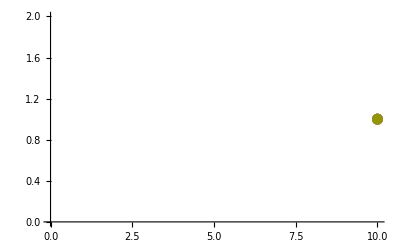

```mathematica
ListPlot[vetores]
```

## Para 9 posições

```mathematica
w=1
h2= ({{0, v, 0, 0, 0, 0, 0, 0, 0}, {v, 0, w, 0, 0, 0, 0, 0, 0}, {0, w, 0, v, 0, 0, 0, 0, 0}, {0, 0, v, 0, w, 0, 0, 0, 0}, {0, 0, 0, w, 0, v, 0, 0, 0}, {0, 0, 0, 0, v, 0, w, 0, 0}, {0, 0, 0, 0, 0, w, 0, v, 0}, {0, 0, 0, 0, 0, 0, v, 0, w}, {0, 0, 0, 0, 0, 0, 0, w, 0}})
```

1

```mathematica
{{0,v,0,0,0,0,0,0,0},{v,0,1,0,0,0,0,0,0},{0,1,0,v,0,0,0,0,0},{0,0,v,0,1,0,0,0,0},{0,0,0,1,0,v,0,0,0},{0,0,0,0,v,0,1,0,0},{0,0,0,0,0,1,0,v,0},{0,0,0,0,0,0,v,0,1},{0,0,0,0,0,0,0,1,0}}
```

```mathematica
(*valores2=Table[Eigenvalues[h2],{v,0.,3.,.1}]*)
```

{{-1.,-1.,-1.,-1.,1.,1.,1.,1.,0.},{1.0825,-1.0825,1.03528,-1.03528,-0.973754,0.973754,0.920976,-0.920976,-7.07062×10^-18},{-1.16774,1.16774,1.07871,-1.07871,-0.957284,0.957284,-0.8464,0.8464,-3.42212×10^-17},{-1.25515,1.25515,-1.12934,1.12934,-0.951099,0.951099,0.777554,-0.777554,-5.79513×10^-18},{1.34433,-1.34433,-1.18626,1.18626,-0.955399,0.955399,-0.716091,0.716091,-1.77858×10^-17},{1.43493,-1.43493,-1.24861,1.24861,-0.970043,0.970043,-0.664066,0.664066,1.58352×10^-17},{-1.5267,1.5267,-1.31561,1.31561,-0.994575,0.994575,-0.623843,0.623843,6.19009×10^-16},{1.61945,-1.61945,-1.38659,1.38659,-1.02829,1.02829,0.59781,-0.59781,-4.38165×10^-16},{1.71302,-1.71302,1.46097,-1.46097,1.07031,-1.07031,-0.587854,0.587854,-3.27659×10^-16},{1.80727,-1.80727,-1.53826,1.53826,-1.11972,1.11972,-0.594785,0.594785,9.74522×10^-16},{1.90211,-1.90211,1.61803,-1.61803,-1.17557,1.17557,-0.618034,0.618034,1.5378×10^-16},{-1.99746,1.99746,-1.69995,1.69995,1.237,-1.237,0.655868,-0.655868,5.81089×10^-17},{-2.09324,2.09324,-1.78372,1.78372,1.30321,-1.30321,0.705946,-0.705946,3.50039×10^-16},{-2.18939,2.18939,-1.86908,1.86908,-1.37352,1.37352,0.765869,-0.765869,-5.96564×10^-16},{-2.28588,2.28588,-1.95582,1.95582,1.44733,-1.44733,-0.833518,0.833518,-7.93122×10^-16},{-2.38266,2.38266,-2.04378,2.04378,1.52412,-1.52412,0.907165,-0.907165,4.18548×10^-16},{2.47969,-2.47969,2.1328,-2.1328,1.60348,-1.60348,-0.985467,0.985467,-3.75413×10^-16},{2.57695,-2.57695,2.22276,-2.22276,1.68503,-1.68503,1.0674,-1.0674,-1.03862×10^-15},{-2.67441,2.67441,-2.31354,2.31354,-1.76848,1.76848,1.15219,-1.15219,3.41846×10^-16},{2.77205,-2.77205,-2.40505,2.40505,-1.85357,1.85357,1.23925,-1.23925,-2.14134×10^-16},{-2.86986,2.86986,-2.49721,2.49721,-1.94009,1.94009,-1.32813,1.32813,8.89535×10^-17},{2.96781,-2.96781,2.58996,-2.58996,-2.02784,2.02784,-1.4185,1.4185,8.38621×10^-16},{-3.06589,3.06589,2.68322,-2.68322,2.11668,-2.11668,-1.51007,1.51007,6.87819×10^-18},{-3.16409,3.16409,2.77695,-2.77695,-2.20647,2.20647,1.60266,-1.60266,-8.51658×10^-16},{-3.2624,3.2624,-2.87111,2.87111,2.29711,-2.29711,1.69609,-1.69609,3.16324×10^-16},{3.36082,-3.36082,2.96565,-2.96565,-2.3885,2.3885,-1.79023,1.79023,-1.45419×10^-15},{3.45932,-3.45932,3.06054,-3.06054,-2.48055,2.48055,-1.88497,1.88497,1.64334×10^-15},{3.55791,-3.55791,-3.15574,3.15574,2.57319,-2.57319,-1.98023,1.98023,-3.30638×10^-16},{-3.65657,3.65657,-3.25123,3.25123,2.66637,-2.66637,-2.07593,2.07593,4.7419×10^-16},{3.7553,-3.7553,-3.34698,3.34698,2.76002,-2.76002,2.17203,-2.17203,-2.16384×10^-15},{3.8541,-3.8541,-3.44298,3.44298,2.8541,-2.8541,2.26846,-2.26846,1.89813×10^-16}}

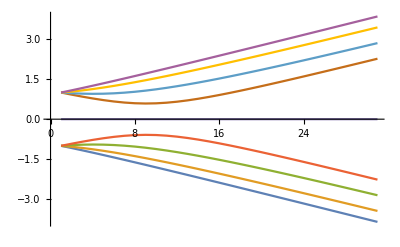

```mathematica
(*ListPlot[(Sort[#]&/@valores2//Transpose),Joined->True]*)
```

```mathematica
{valores2,vetores2}=Eigensystem[h2]
```

{{0,-(√(2-v-√5 v+2 v^2))/(√2),(√(2-v-√5 v+2 v^2))/(√2),-(√(2+v-√5 v+2 v^2))/(√2),(√(2+v-√5 v+2 v^2))/(√2),-(√(2-v+√5 v+2 v^2))/(√2),(√(2-v+√5 v+2 v^2))/(√2),-(√(2+v+√5 v+2 v^2))/(√2),(√(2+v+√5 v+2 v^2))/(√2)},{{1/v^4,0,-1/v^3,0,1/v^2,0,-1/v,0,1},{-v,(√(2-v-√5 v+2 v^2))/(√2),1/2 (-2+v+√5 v),1/4 (-√2 √(2-v-√5 v+2 v^2)-√10 √(2-v-√5 v+2 v^2)),1/2 (1+√5-v-√5 v),1/4 (√2 √(2-v-√5 v+2 v^2)+√10 √(2-v-√5 v+2 v^2)),1/2 (-1-√5+2 v),-(√(2-v-√5 v+2 v^2))/(√2),1},{-v,-(√(2-v-√5 v+2 v^2))/(√2),1/2 (-2+v+√5 v),1/4 (√2 √(2-v-√5 v+2 v^2)+√10 √(2-v-√5 v+2 v^2)),1/2 (1+√5-v-√5 v),1/4 (-√2 √(2-v-√5 v+2 v^2)-√10 √(2-v-√5 v+2 v^2)),1/2 (-1-√5+2 v),(√(2-v-√5 v+2 v^2))/(√2),1},{v,-(√(2+v-√5 v+2 v^2))/(√2),1/2 (2+v-√5 v),1/4 (-√2 √(2+v-√5 v+2 v^2)+√10 √(2+v-√5 v+2 v^2)),1/2 (1-√5+v-√5 v),1/4 (-√2 √(2+v-√5 v+2 v^2)+√10 √(2+v-√5 v+2 v^2)),1/2 (1-√5+2 v),-(√(2+v-√5 v+2 v^2))/(√2),1},{v,(√(2+v-√5 v+2 v^2))/(√2),1/2 (2+v-√5 v),1/4 (√2 √(2+v-√5 v+2 v^2)-√10 √(2+v-√5 v+2 v^2)),1/2 (1-√5+v-√5 v),1/4 (√2 √(2+v-√5 v+2 v^2)-√10 √(2+v-√5 v+2 v^2)),1/2 (1-√5+2 v),(√(2+v-√5 v+2 v^2))/(√2),1},{-v,(√(2-v+√5 v+2 v^2))/(√2),1/2 (-2+v-√5 v),1/4 (-√2 √(2-v+√5 v+2 v^2)+√10 √(2-v+√5 v+2 v^2)),1/2 (1-√5-v+√5 v),1/4 (√2 √(2-v+√5 v+2 v^2)-√10 √(2-v+√5 v+2 v^2)),1/2 (-1+√5+2 v),-(√(2-v+√5 v+2 v^2))/(√2),1},{-v,-(√(2-v+√5 v+2 v^2))/(√2),1/2 (-2+v-√5 v),1/4 (√2 √(2-v+√5 v+2 v^2)-√10 √(2-v+√5 v+2 v^2)),1/2 (1-√5-v+√5 v),1/4 (-√2 √(2-v+√5 v+2 v^2)+√10 √(2-v+√5 v+2 v^2)),1/2 (-1+√5+2 v),(√(2-v+√5 v+2 v^2))/(√2),1},{v,-(√(2+v+√5 v+2 v^2))/(√2),1/2 (2+v+√5 v),1/4 (-√2 √(2+v+√5 v+2 v^2)-√10 √(2+v+√5 v+2 v^2)),1/2 (1+√5+v+√5 v),1/4 (-√2 √(2+v+√5 v+2 v^2)-√10 √(2+v+√5 v+2 v^2)),1/2 (1+√5+2 v),-(√(2+v+√5 v+2 v^2))/(√2),1},{v,(√(2+v+√5 v+2 v^2))/(√2),1/2 (2+v+√5 v),1/4 (√2 √(2+v+√5 v+2 v^2)+√10 √(2+v+√5 v+2 v^2)),1/2 (1+√5+v+√5 v),1/4 (√2 √(2+v+√5 v+2 v^2)+√10 √(2+v+√5 v+2 v^2)),1/2 (1+√5+2 v),(√(2+v+√5 v+2 v^2))/(√2),1}}}

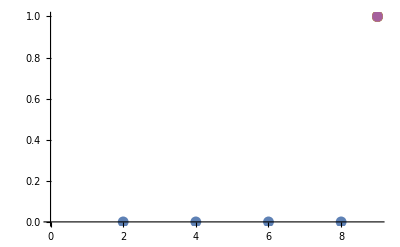

```mathematica
ListPlot[vetores2]
```